Copyright ©, 2015, Erdong Guo and Shu Lin
Author: Erdong Guo and Shu Lin
E-mail: guoerdong@itp.ac.cn, linshu8@mail.sysu.edu.cn
Affliation: Institute of Theoretical Physics, Chinese Academy of Scineces, School of Physics and Astronomy, Sun-Yat Sen University
Description: Calculation tools for AdS/QCD. In this file, we calculate the axial current in the field theory which corresponds to a integral in the bulk. J^{\mu}_5 = ∫δS/(δ∂_μ ϕ)ⅆρ

```mathematica
Quit[];
```

```mathematica
H=1+1/#^4&;f=1-1/#^4&;
gtt=-r0^2/2 #^2 f[#]^2/H[#]&;
gxx=r0^2/2 #^2 H[#]&;
gthethe=1;
gphiphi= chi[#]^2&;
gss=1-chi[#]^2&;
grhorho=1/#^2&;
```

```mathematica
$Assumptions=And[rho>1,chi[rho]>0,chi[rho]<1,r0>0,B>0];
```

```mathematica
L=Sqrt[-gtt[rho](grhorho[rho](1-chi[rho]^2)+chi'[rho]^2)-(1-chi[rho]^2)At'[rho]^2]Sqrt[gxx[rho](gxx[rho]^2+B^2)](1-chi[rho]^2);
```

```mathematica
sq1[rho]=√(-(gss[rho]^4 gxx[rho] (B^2+gxx[rho]^2))/(gss[rho] (grhorho[rho] gtt[rho]+At'[rho]^2)+gthethe gtt[rho] chi'[rho]^2));
```

```mathematica
eq1=6 aa[rho]^2 √gphiphi[rho] gxx[rho] (dd[rho]^2 gss[rho]+gthethe gtt[rho] chi'[rho]^2)^2+gthethe (bb[rho]^2 gss[rho] gtt[rho] chi'[rho] (gss[rho] dd[rho]^2+gthethe gtt[rho] chi'[rho]^2) gxx'[rho]+aa[rho]^2 gxx[rho] (3 gthethe gtt[rho]^2 chi'[rho]^3 gss'[rho]+gss[rho] gtt[rho] chi'[rho] (2 dd[rho]^2 gss'[rho]+gthethe chi'[rho]^2 gtt'[rho])+gss[rho]^2 (chi'[rho] (-gtt[rho]^2 grhorho'[rho]+grhorho[rho] gtt[rho] gtt'[rho]+2 At'[rho]^2 gtt'[rho]-2 gtt[rho] At'[rho] At''[rho])+2 dd[rho]^2 gtt[rho] chi''[rho])));
eq2=D[sq1[rho]At'[rho],rho];
```

```mathematica
reph={a2->-3/4 a0^2 (-1+b2^2),a3->1/4 a0 (2+a0) (-1+b2^2),b3->-1/(16 (-1+a0^2) (1+B^2))b2 (18 a0^3 (1+B^2) (-1+b2^2)^2+9 a0^4 (1+B^2) (-1+b2^2)^2+4 (-3+6 b2^2+B^2 (1+2 b2^2))-4 a0^2 (-3+6 b2^2+B^2 (1+2 b2^2))),b4->1/(40 (-1+a0^2) (1+B^2))b2 (102 a0^3 (1+B^2) (-1+b2^2)^2+9 a0^4 (1+B^2) (-1+b2^2)^2+20 (-5+6 b2^2+B^2 (-1+2 b2^2))+4 a0^2 (31-42 b2^2+6 b2^4+B^2 (11-22 b2^2+6 b2^4)))};
repp={aa[rho]^2->B^2+gxx[rho]^2,bb[rho]^2->B^2+3gxx[rho]^2,dd[rho]^2->grhorho[rho]gtt[rho]+At'[rho]^2};
```

```mathematica
eps=1/100;uv=100;
NDSolve[{eq1==0,eq2==0,chi[1+eps]==a0+a2 eps^2+a3 eps^3 ,chi'[1+eps]== 2a2 eps+3a3 eps^2,At[1+eps]== b0+b2 eps^2-b2 eps^3+b3 eps^4+b4 eps^5,At'[1+eps]==2b2 eps-3b2 eps^2+4 b3 eps^3+5 b4 eps^4}/.reph/.repp/.{r0->1,B->1,a0->3/4,b0->0,b2->1/2},{chi,At},{rho,1+eps,uv},Method->{"EquationSimplification"->"Solve"}][[1]]
```

{chi→InterpolatingFunction[{{1.01,100.}},<>],At→InterpolatingFunction[{{1.01,100.}},<>]}

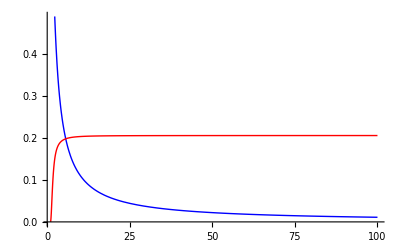

```mathematica
Plot[{chi[rho]/.%,At[rho]/.%},{rho,1+eps,uv},PlotStyle->{Blue,Red}]
```

```mathematica
mum[aa0_,bb2_,BB_,eps_,uv_]:=
Module[{sol,data,rep,mm,cc},
sol=NDSolve[{eq1==0,eq2==0,chi[1+eps]==a0+a2 eps^2+a3 eps^3 ,chi'[1+eps]== 2a2 eps+3a3 eps^2,At[1+eps]== b0+b2 eps^2-b2 eps^3+b3 eps^4+b4 eps^5,At'[1+eps]==2b2 eps-3b2 eps^2+4 b3 eps^3+5 b4 eps^4}/.reph/.repp/.{b0->0}/.{r0->1,a0->aa0,b2->bb2,B->BB},{chi,At},{rho,1+eps,uv},Method->{"EquationSimplification"->"Solve"},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->25][[1]];
data=Table[{rho,rho chi[rho]/.sol[[1]]}/.{rho->uv-i},{i,5}];
rep=FindFit[data,mm+cc/rho^2,{mm,cc},rho];
(*j5=NIntegrate[((1-chi[rho]^2)^2B At'[rho])/.sol/.{B->BB},{rho,1+eps,uv},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->25];*)
{uv chi[uv]/.sol,cc/.rep,(At[uv]-At[1+eps])/.sol}]
```

testing the uv and ir sensity

```mathematica
mum[0,1/20,1/2,100,1/100]
```

{0,0.,0.0269149711644778475338056}

```mathematica
tmum[0,1/20,1/2,50,1/100]
```

{0,0.,0.0268981796555073525922981}

```mathematica
tmum[0,1/20,1/2,200,1/100]
```

{0,0.,0.02691916904268572817827}

```mathematica
rephm={a1->-((-1+rr^4) (4 B^2 rr^4+r0^4 (1+rr^4)^2))/((rr+rr^5) (2 B^2 rr^4+r0^4 (1+rr^8))),a2->(rr^2 (r0^8 rr^4 (1+rr^4)^2 (-17+3 rr^8)+2 B^4 rr^4 (3-46 rr^4+15 rr^8)+B^2 r0^4 (9-50 rr^4-60 rr^8-38 rr^12+27 rr^16)))/(3 (1+rr^4)^2 (2 B^2 rr^4+r0^4 (1+rr^8))^2)};
```

```mathematica
eps=1/100;uv=100;
NDSolve[{eq1==0,eq2==0,chi[rr+eps]==1+a1 eps+a2 eps^2 ,chi'[rr+eps]==a1+2a2 eps,At[rr+eps]== b0,At'[rr+eps]==0}/.repp/.rephm/.{r0->1,B->1,rr->1,b0->1},{chi,At},{rho,1+eps,uv},Method->{"EquationSimplification"->"Solve"}][[1]]
```

{chi→InterpolatingFunction[{{1.01,100.}},<>],At→InterpolatingFunction[{{1.01,100.}},<>]}

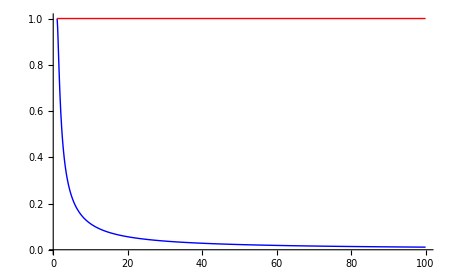

```mathematica
Plot[{chi[rho]/.%,At[rho]/.%},{rho,1+eps,uv},PlotStyle->{Blue,Red}]
```

```mathematica
mmum[rr0_,bb0_,BB_,eps_,uv_]:=
Module[{sol,rep,data,mm,cc},
sol=NDSolve[{eq1==0,eq2==0,chi[rr+eps]==1+a1 eps+a2 eps^2 ,chi'[rr+eps]==a1+2a2 eps,At[rr+eps]== b0,At'[rr+eps]==0}/.repp/.rephm/.{b0->bb0}/.{r0->1,rr->rr0,B->BB},{chi,At},{rho,rr0+eps,uv},Method->{"EquationSimplification"->"Solve"},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->25][[1]];
data=Table[{rho,rho chi[rho]/.sol[[1]]}/.{rho->uv-i},{i,5}];
rep=FindFit[data,mm+cc/rho^2,{mm,cc},rho];
(*j5=NIntegrate[((1-chi[rho]^2)^2B At'[rho])/.sol/.{B->BB},{rho,rr0+eps,uv},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->25];*)
{uv chi[uv]/.sol,cc/.rep,At[uv]/.sol}]
```

```mathematica
mmum[101/100,1/2,1,100,1/100]
```

{1.12197034002270269099108,0.504129924485786552544976,0.5}

```mathematica
repb={chi->Function[rho,m/rho+c/rho^3],At->Function[rho,b0+b2/rho^2]};
```

```mathematica
Series[L/.repb/.{r0->1},{rho,Infinity,1}]//FullSimplify
```

rho^3/4-(m^2 rho)/4+B^2/(2 rho)+O[1/rho]^2

```mathematica
Lbd=rho^3/4-(m^2 rho)/4+B^2/(2 rho);
```

```mathematica
FEB[Chi0_,bb2_,BB_,eps_,uv_]:=
Module[{sol,data,rep,FE,mm,cc},
sol=NDSolve[{eq1==0,eq2==0,chi[1+eps]==a0+a2 eps^2+a3 eps^3 ,chi'[1+eps]== 2a2 eps+3a3 eps^2,At[1+eps]== b0+b2 eps^2-b2 eps^3+b3 eps^4+b4 eps^5,At'[1+eps]==2b2 eps-3b2 eps^2+4 b3 eps^3+5 b4 eps^4}/.reph/.repp/.{b0->0}/.{r0->1,a0->Chi0,b2->bb2,B->BB},{chi,At},{rho,1+eps,uv},Method->{"EquationSimplification"->"Solve"},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->25][[1]];data=Table[{rho,rho chi[rho]/.sol[[1]]}/.{rho->uv-i},{i,5}];
rep=FindFit[data,mm+cc/rho^2,{mm,cc},rho];
{1/mm/.rep,(At[uv]-At[1+eps])/.sol,FE=NIntegrate[L/.sol/.rep/.{B->BB,r0->1},{rho,1+eps,uv},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->25]-(1/16(((uv^2-mm^2)^2-4 mm cc)/.rep)+B^2/2 Log[uv]/.{B->BB})}]
```

```mathematica
FEB[1/2,1/2,1,1/100,100]
```

{1.24897418202288100984983,-0.41701558477576815}

```mathematica
FEB[4/5,1/2,1,1/100,100]
```

{0.873426483604294614228276,-0.40369751397491937}

```mathematica
FEM[rr0_,bb0_,BB_,eps_,uv_]:=
Module[{sol,data,rep,mm,cc,FE},
sol=NDSolve[{eq1==0,eq2==0,chi[rr+eps]==1+a1 eps+a2 eps^2 ,chi'[rr+eps]==a1+2a2 eps,At[rr+eps]== b0,At'[rr+eps]==0}/.repp/.rephm/.{b0->bb0}/.{r0->1,rr->rr0,B->BB},{chi,At},{rho,rr0+eps,uv},Method->{"EquationSimplification"->"Solve"},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->25][[1]];
data=Table[{rho,rho chi[rho]/.sol}/.{rho->uv-i},{i,5}];
rep=FindFit[data,mm+cc/rho^2,{mm,cc},rho];
{1/mm/.rep,bb0,FE=NIntegrate[L/.sol/.rep/.{B->BB,r0->1},{rho,rr0+eps,uv},AccuracyGoal->16,PrecisionGoal->16,WorkingPrecision->25]-(1/16(((uv^2-mm^2)^2-4 mm cc)/.rep)+B^2/2 Log[uv]/.rep/.{B->BB})}]
```

```mathematica
FEM[2,1/2,2,1/100,100]
```

{0.607062679885427465004853,-2.18122120037646717}

```mathematica
FEM[2,1/2,2,1/100,200]
```

{0.607062686245711433222052,-2.181484150979767}

```mathematica
FEM[2,1/2,2,1/100,50]
```

{0.607062563313018792688415,-2.180165696894210183}

```mathematica
FEM[2,1/2,2,1/50,100]
```

{0.607059003651267566503185,-2.18187015597785266}

```mathematica
data=Table[{mum[i/21,1/2,0,1/100,100][[1]],mum[i/21,1/2,0,1/100,100][[3]]},{i,1,20}];
```

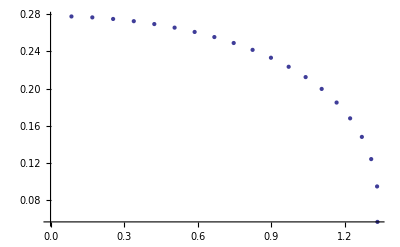

```mathematica
ListPlot[data]
```

```mathematica
data=Table[{mum[i/21,1/2,0,1/100,100][[1]],mum[i/21,1/2,0,1/100,100][[3]]/mum[i/21,1/2,0,1/100,100][[1]]},{i,1,20}];
```

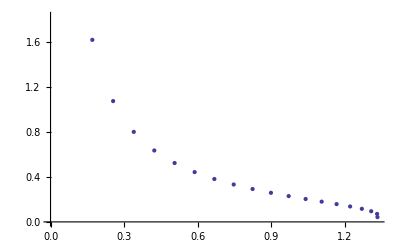

```mathematica
ListPlot[data]
```

```mathematica
data=Table[{mum[1/20,i/200,0,1/100,100][[1]],mum[1/20,i/200,0,1/100,100][[3]]/mum[1/20,i/200,0,1/100,100][[1]]},{i,1,20}];
```

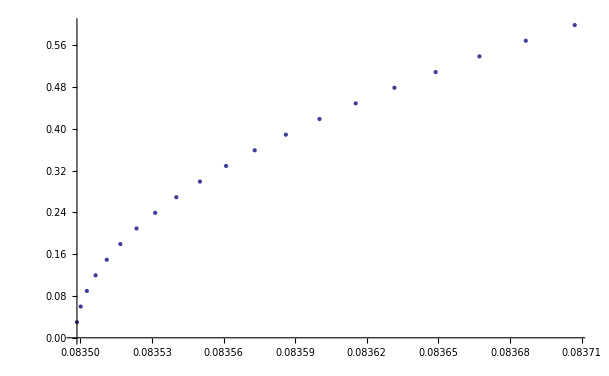

```mathematica
ListPlot[data]
```

```mathematica
dataa[ini_,ii_]:=
Module[{data},
data=Table[{mum[ini/20,i/200,0,1/100,100][[1]],mum[ini/20,i/200,0,1/100,100][[3]]/mum[ini/20,i/200,0,1/100,100][[1]]},{i,1,ii}];
ListPlot[data]]
```

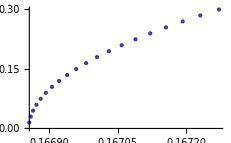
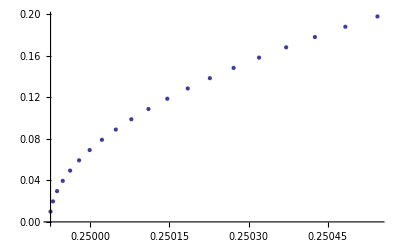
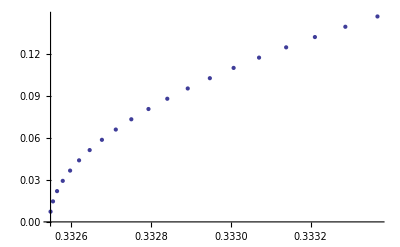
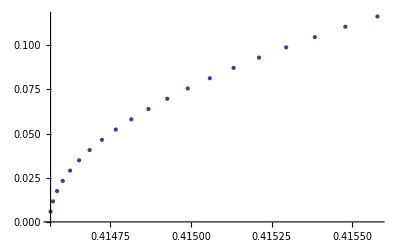
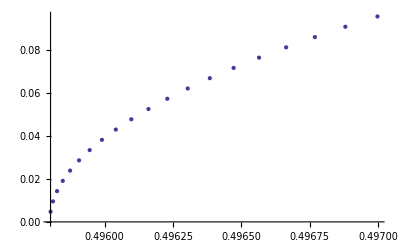
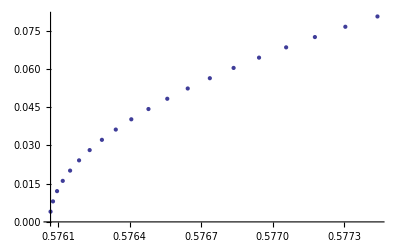
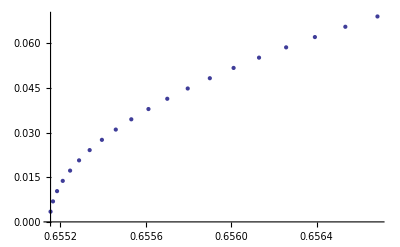
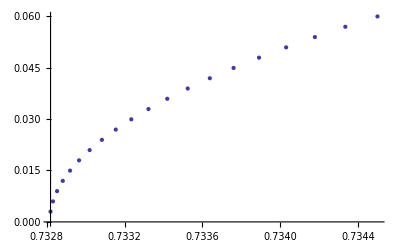

```mathematica
Table[dataa[1+i,20],{i,1,10}]
```

```mathematica
data=Table[mum[i/21,j/200,0,1/100,100][[1]],{i,0,20},{j,0,20}];
```

```mathematica
ListPlot3D[data,AxesLabel->{At,chi}]
```

-Graphics3D-

```mathematica
data=Table[mum[i/20,j/20,0,1/100,100][[1]],{i,0,19},{j,0,20}];
```

```mathematica
ListPlot3D[data,AxesLabel->{At,chi},PlotRange->All]
```

-Graphics3D-

```mathematica
phadig[initb_,nb_,nm_,ab_,am_,stplb_,stplm_]:=
Module[{datab,datam,mumb,mumm},
datab=Table[{FEB[initb+i stplb,ab,0,1/100,100][[1]],FEB[initb+i stplb,ab,0,1/100,100][[3]]},{i,0,nb}];
datam=Table[{FEM[1+i stplm,am,0,1/100,100][[1]],FEM[1+i stplm,am,0,1/100,100][[3]]},{i,0,nm}];
mumb=Table[{FEB[initb+i stplb,ab,0,1/100,100][[1]],FEB[initb+i stplb,ab,0,1/100,100][[2]] FEB[initb+i stplb,ab,0,1/100,100][[1]]},{i,0,nb}];
mumm=Table[{FEM[1+i stplm,am,0,1/100,100][[1]],FEM[1+i stplm,am,0,1/100,100][[2]]FEM[1+i stplm,am,0,1/100,100][[1]]},{i,0,nm}];
{ListLinePlot[{datab,datam},PlotStyle->{Red,Blue}],ListLinePlot[{mumb,mumm},PlotStyle->{Red,Blue}]}]
```

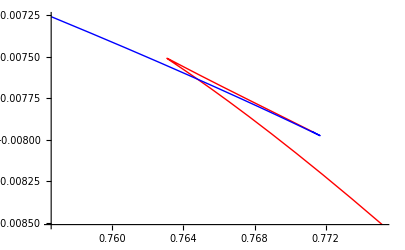
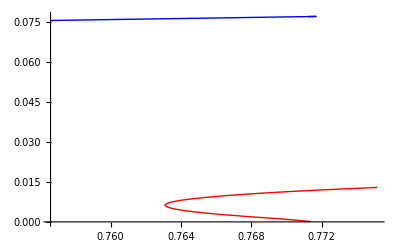

```mathematica
phadig[9/10,20,20,1/10,1/10,1/201,1/100]
```

```mathematica
phadig[9/10,20,20,5/10,1/10,1/201,1/100]
```

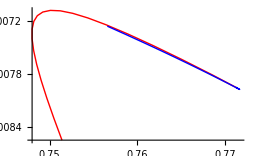
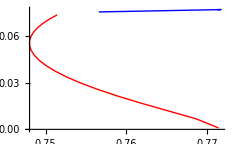

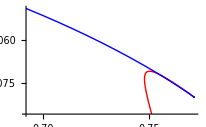
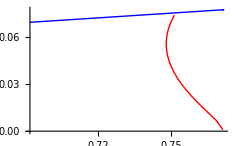

```mathematica
phadig[9/10,20,20,5/10,1/10,1/201,1/50]
```

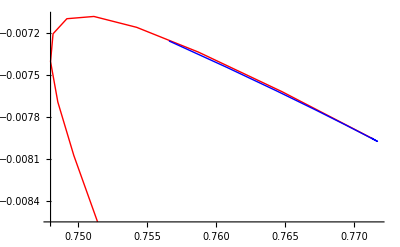
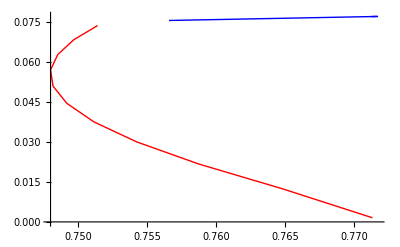

```mathematica
phadig[9/10,10,10,5/10,1/10,1/101,1/50]
```

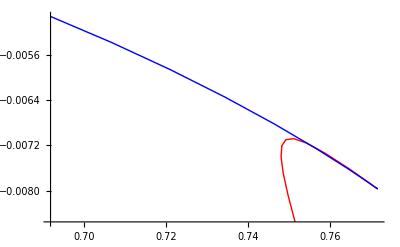
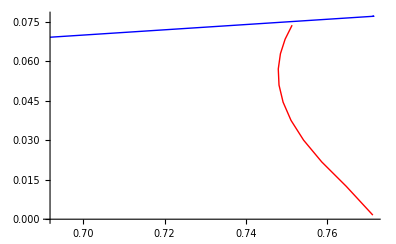

```mathematica
phadig[9/10,10,10,5/10,1/10,1/101,1/25]
```

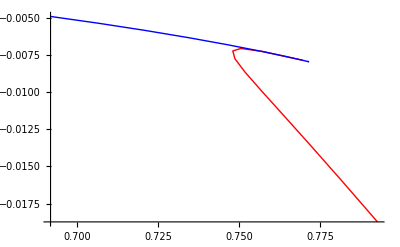
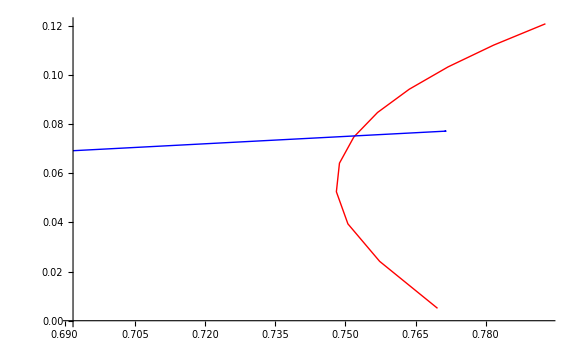

```mathematica
phadig[8/10,10,10,5/10,1/10,1/51,1/25]
```

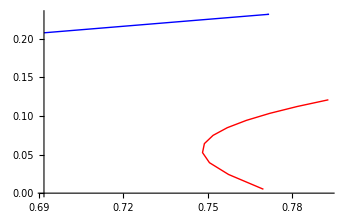
{-Graphics-,-Graphics-}

```mathematica
phadig[8/10,10,10,5/10,3/10,1/51,1/25]
```

```mathematica
Table[{phadig[9/10,20,20,1/10,i/10,1/201,1/100]},{i,2,4}]
```

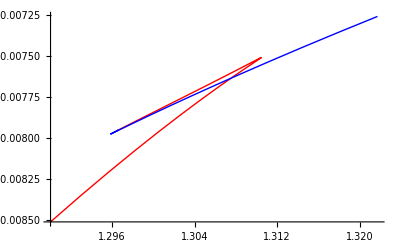
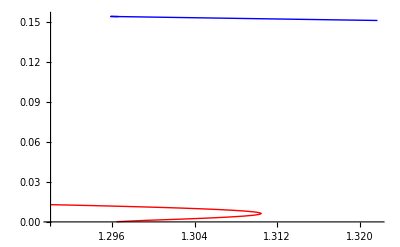
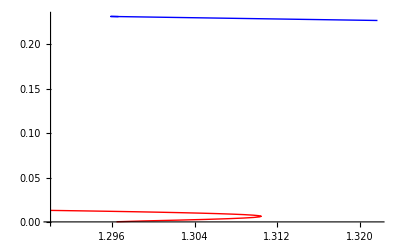
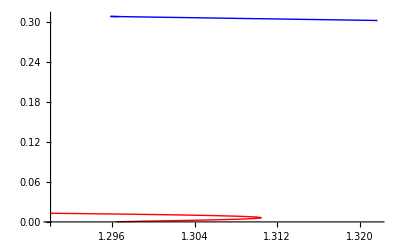
```mathematica
{{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-}}}
```

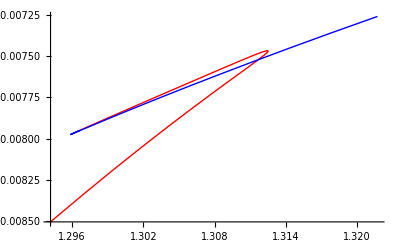
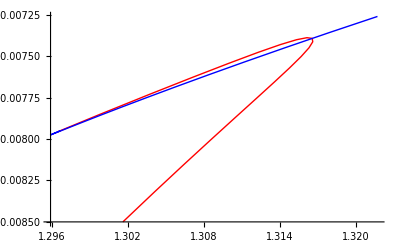
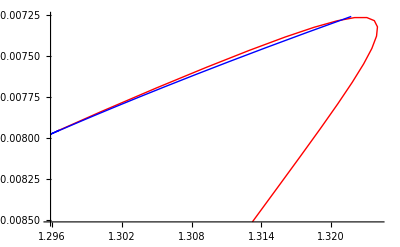
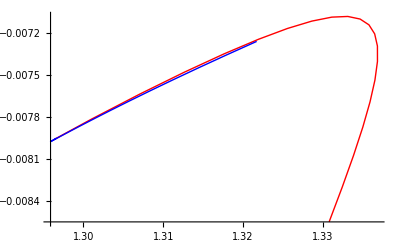

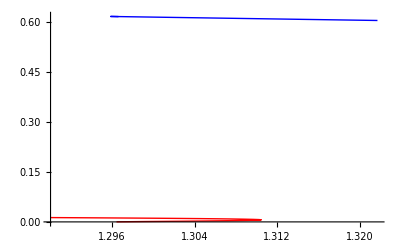
{-Graphics-,-Graphics-}

```mathematica
phadig[9/10,10,10,1/10,4/5,1/101,1/50]
```

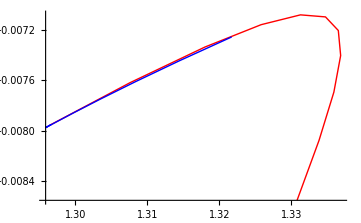
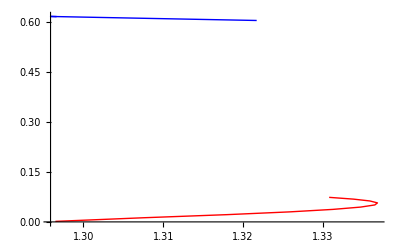

```mathematica
phadig[9/10,10,10,5/10,4/5,1/101,1/50]
```

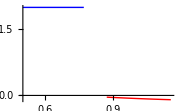
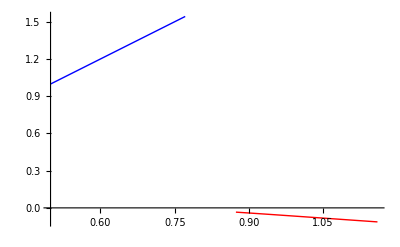

```mathematica
phadig[5/10,10,10,5/10,2,1/51,1/10]
```

```mathematica
phadig[5/10,10,10,5/10,2,1/51,1/10]
```

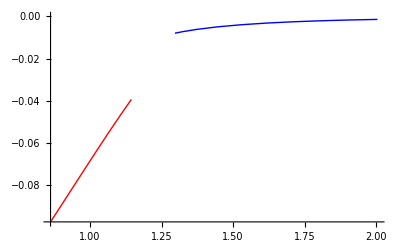
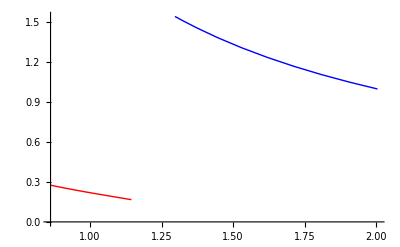

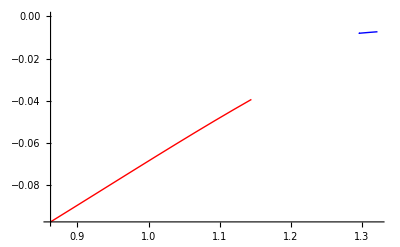
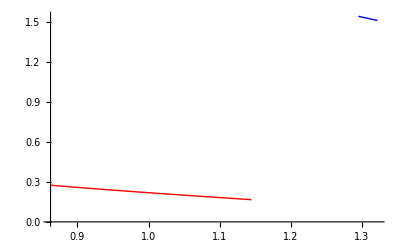

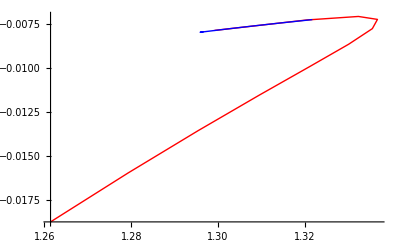
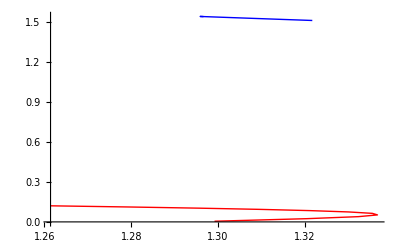

```mathematica
phadig[5/10,10,10,5/10,2,1/51,1/10]
```

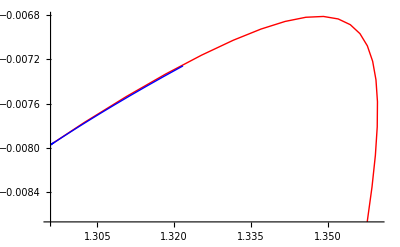
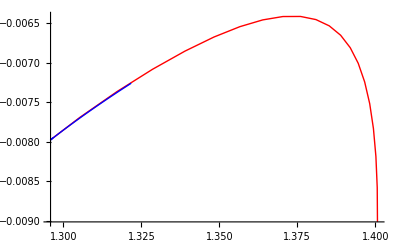
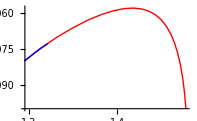

```mathematica
Table[{phadig[9/10,20,20,i/10,i/10,1/201,1/100]},{i,6,8}]
```

```mathematica
Table[{phadig[9/10,20,20,1/10,i/10,1/201,1/100]},{i,6,8}]
```

{{{-Graphics-}},{{-Graphics-}},{{-Graphics-}}}